#### Polynomial Regression by Gradient Descent Kirill Zakharov

```mathematica
gradDescent[f_,X_,Y_,θ_,η_,ϵ_,k_]:=Module[{t,vars,g,rule,grad,points=θ,sol},
vars=Table[m[i],{i,Length@θ}];
g=Grad[f[vars,X,Y],vars]//Simplify;

rule=Rule@@@Transpose[{vars,points}];
grad=g/.rule;
sol=points-η×grad;
t=1;
While[Abs[f[sol,X,Y]-f[points,X,Y]]>ϵ &&t<k,
points=sol;
rule=Rule@@@Transpose[{vars,points}];
grad=g/.rule;
sol=points-η×grad;
t++
];
{sol,f[sol,X,Y]}
]
```

```mathematica
k=100;
dataX=Table[Random[],k];
dataY=Cos[1.5Pi #]&/@dataX;
newY=dataY+RandomReal[{0,1},k]*0.2;
```

```mathematica
p[coef_,x_]:=Total[coef*Table[x^i,{i,0,Length@coef-1}]]
```

```mathematica
funQ[q_,X_,Y_]:=Total[(p[q,#]&/@X-Y)^2]
```

```mathematica
gradDescent[funQ,dataX,newY,{0,0,0},0.005,10^-5,1000];
```

#### Cross-Validation

Generate data

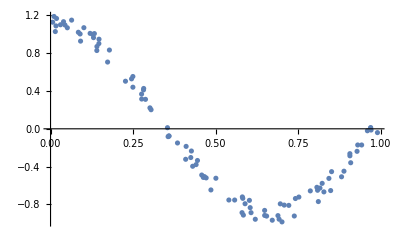

```mathematica
dataX1=RandomReal[{0,1},k];
dataY1=Cos[1.5 π dataX1]+RandomReal[{0,1},k]*0.2;
ListPlot[Thread[{dataX1,dataY1}]]
```

Split in 4 groups

```mathematica
gr=4;
step=k/gr;
data=Transpose[{dataX1,dataY1}];
```

```mathematica
folds=Table[data⟦i;;i+step-1⟧,{i,1,k,step}];
```

```mathematica
Length@folds
```

4

```mathematica
crossValidation[folds_,θ_]:=Module[{train,test,i,results,mean,coef,objF,e,testX,testY,trainX,trainY},
train=folds⟦1⟧;
test=folds⟦2⟧;
i=2;
results={};
Do[
{trainX,trainY}=Transpose@train;
{testX,testY}=Transpose@test;
{coef,objF}=gradDescent[funQ,trainX,trainY,θ,0.005,10^-5,1000];
AppendTo[results,funQ[coef,testX,testY]];
train=Join[train,test];
test=folds⟦i⟧,
{i,2,Length@folds}
];
{results,results//Mean}
]
```

```mathematica
res=crossValidation[folds,#]&/@Table[0,{j,1,7},{i,1,j}];
res
```

{{{9.35695,7.95641,12.0528},9.78872},{{6.3719,4.77022,5.82979},5.6573},{{2.89008,1.24857,0.957435},1.6987},{{0.776957,0.342557,0.386147},0.501887},{{0.301693,0.238681,0.273759},0.271377},{{0.324888,0.317997,0.330564},0.324483},{{0.495051,0.410403,0.383356},0.429603}}

```mathematica
coeff=res[[All,2]];
```

Find the best degree

```mathematica
bestDegree={Position[coeff,Min[coeff]],Min[coeff]}
```

{{{5}},0.271377}

#### Final Result

```mathematica
{coeffF,objF}=gradDescent[funQ,dataX,newY,ConstantArray[0,First@Flatten@bestDegree],0.005,10^-5,1000];
```

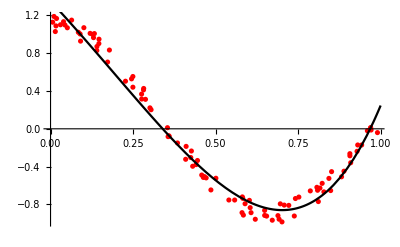

```mathematica
Show[ListPlot[data,PlotStyle->Red],Plot[p[coeffF,x],{x,0,1},PlotStyle->Black]]
```

```mathematica
p[coeffF,x]
```

1.35185-3.7675 x-1.3645 x^2+1.22709 x^3+2.79975 x^4